## Real spherical harmonics Y_lm

```mathematica
ClearAll["Global`*"]
```

Define a custom style for outputting data

```mathematica
style[object_,xcolor_]:=Style[object,xcolor,19,FontFamily->"Times",Bold];
```

Transform from degrees into radians

```mathematica
rad[x_]:=x*π/180;
deg[x_]:=x*180/π;
```

Path of the local env

```mathematica
path="/Users/robertpoenaru/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DevWorkspace/Github/physics-code-collection/Code-Collection/Spherical-Harmonics";
```

### Creating the standard expressions for the spherical harmonics for a given orbital quantum number l

```mathematica
YLM[l_,m_]:=SphericalHarmonicY[l,m,θ,φ];
harmonicSet[l_]:=Table[YLM[l,k],{k,-l,l,1}];
(*create the expressionf for Y_(20,2-2,02,)*)
q2HarmonicSet=Table[{StringTemplate["Y_2.(θ , φ) = "][k],YLM[2,k]},{k,-2,2,2}];
```

Standard expressions Y_lm(θ,φ)

```mathematica
Do[Print[style[q2HarmonicSet[[i]][[1]],Red],"",style[q2HarmonicSet[[i]][[2]],Blue]],{i,1,Length[q2HarmonicSet]}]
```

Y_(2-2)(θ , φ) = 1/4 ⅇ^(-2 ⅈ φ) √(15/(2 π)) Sin[θ]^2

Y_20(θ , φ) = 1/4 √(5/π) (-1+3 Cos[θ]^2)

Y_22(θ , φ) = 1/4 ⅇ^(2 ⅈ φ) √(15/(2 π)) Sin[θ]^2

### Creating the representation of the spherical harmonics in terms of a real basis -Graphics-

```mathematica
YLMRealBasis[l_,m_]:={Sqrt[2]*(-1)^m Im[YLM[l,Abs[m]]],YLM[l,0],Sqrt[2]*(-1)^m Re[YLM[l,m]]};
YLMComplexBasis[l_,m_]:={1/Sqrt[2](YLM[l,Abs[m]]-I*YLM[l,-Abs[m]]),YLM[l,0],(-1)^m/Sqrt[2](YLM[l,Abs[m]]+I*YLM[l,-Abs[m]])};
RealYLM[l_,m_]:=If[m<0,YLMRealBasis[l,m][[1]],If[m>0,YLMRealBasis[l,m][[3]],YLMRealBasis[l,m][[2]]]];
ComplexYLM[l_,m_]:=If[m<0,YLMComplexBasis[l,m][[1]],If[m>0,YLMComplexBasis[l,m][[3]],YLMComplexBasis[l,m][[2]]]];
```

```mathematica
Do[Print[style[StringTemplate["Y_2.^Real = "][k],Black],style[RealYLM[2,k],Black],style[StringTemplate["\n  Y_2.^Im = "][k],Red],style[ComplexYLM[2,k],Red]],{k,-2,2,2}]
```

Y_(2-2)^Real = 1/4 √(15/π) Im[ⅇ^(2 ⅈ φ) Sin[θ]^2]
  Y_(2-2)^Im = (-1/4 ⅈ ⅇ^(-2 ⅈ φ) √(15/(2 π)) Sin[θ]^2+1/4 ⅇ^(2 ⅈ φ) √(15/(2 π)) Sin[θ]^2)/(√2)

Y_20^Real = 1/4 √(5/π) (-1+3 Cos[θ]^2)
  Y_20^Im = 1/4 √(5/π) (-1+3 Cos[θ]^2)

Y_22^Real = 1/4 √(15/π) Re[ⅇ^(2 ⅈ φ) Sin[θ]^2]
  Y_22^Im = (1/4 ⅈ ⅇ^(-2 ⅈ φ) √(15/(2 π)) Sin[θ]^2+1/4 ⅇ^(2 ⅈ φ) √(15/(2 π)) Sin[θ]^2)/(√2)

## Plot the real part of the spherical harmonics for l=2 -> φ is fixed

Y_22

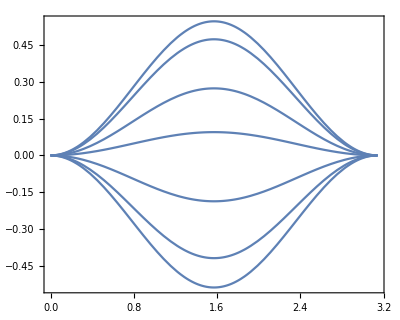

```mathematica
Plot[Table[RealYLM[2,2]/.{φ->k},{k,rad[0],rad[360],rad[55]}],{θ,0,π},PlotStyle->Automatic,AspectRatio->0.8,Frame->True,Axes->False]
```

Y_(2-2)

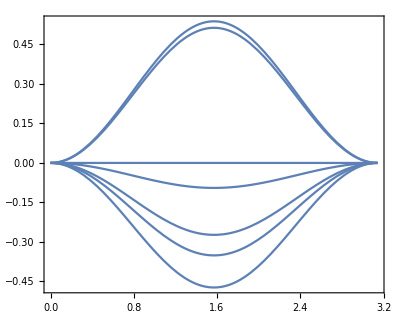

```mathematica
Plot[Table[RealYLM[2,-2]/.{φ->k},{k,rad[0],rad[360],rad[55]}],{θ,0,π},PlotStyle->Automatic,AspectRatio->0.8,Frame->True,Axes->False,PlotRange->Full]
```

Y_20

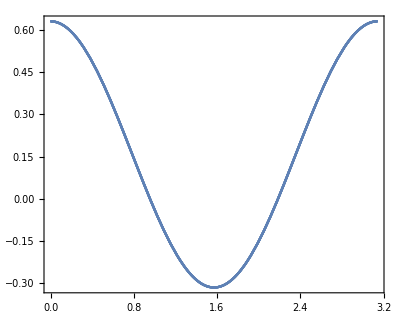

```mathematica
Plot[Table[RealYLM[2,0]/.{φ->k},{k,rad[0],rad[360],rad[55]}],{θ,0,π},PlotStyle->Automatic,AspectRatio->0.8,Frame->True,Axes->False]
```

## Plot the real part of the spherical harmonics for l=2 -> θ is fixed

Y_22

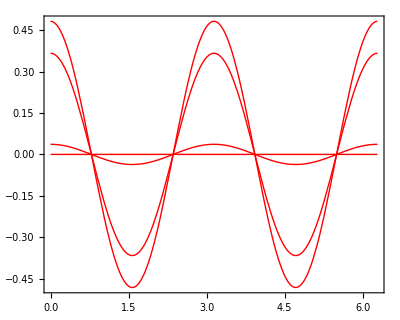

```mathematica
Plot[Table[RealYLM[2,2]/.{θ->k},{k,rad[0],rad[180],rad[55]}],{φ,0,2π},PlotStyle->{Red,Thick},AspectRatio->0.8,Frame->True,Axes->False]
```

Y_(2-2)

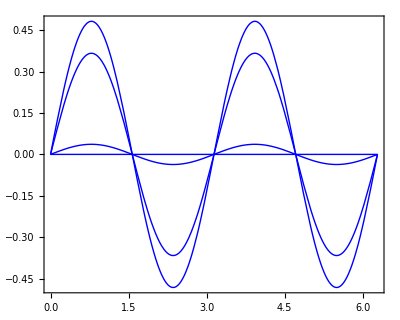

```mathematica
Plot[Table[RealYLM[2,-2]/.{θ->k},{k,rad[0],rad[180],rad[55]}],{φ,0,2π},PlotStyle->{Blue,Thick},AspectRatio->0.8,Frame->True,Axes->False]
```

Y_20

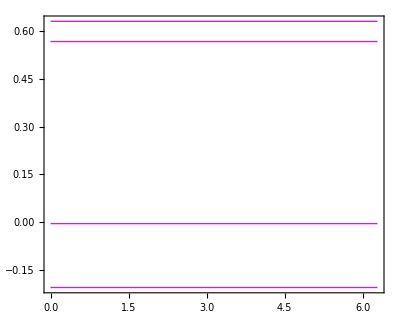

```mathematica
Plot[Table[RealYLM[2,0]/.{θ->k},{k,rad[0],rad[180],rad[55]}],{φ,0,2π},PlotStyle->{Magenta,Thick},AspectRatio->0.8,Frame->True,Axes->False]
```

## 3D representation of the spherical harmonics of given l=2

```mathematica
figTuple={RealYLM[2,0],RealYLM[2,2],RealYLM[2,-2]};
spherical=SphericalPlot3D[{figTuple[[1]],figTuple[[2]],figTuple[[3]]},{θ,0,π},{φ,0,2π},PlotRange->Full];
plotF[fig_,file_]:=Export[StringTemplate["``/``.pdf"][path,file],fig];
plotF[spherical,"realHarmonics"];
Show[spherical]
```

-Graphics3D-

### Create a graphical representation for a function expressed in terms of Spherical Harmonics (real basis for the spherical functions)

```mathematica
(*Test parameters for the V-function*)
f=Sqrt[2];
g=12;
thetaMin=rad[90];
phiMin=rad[180];
VFunction[f_,g_]:=f*RealYLM[2,0]+g(RealYLM[2,2]+RealYLM[2,-2]);
```

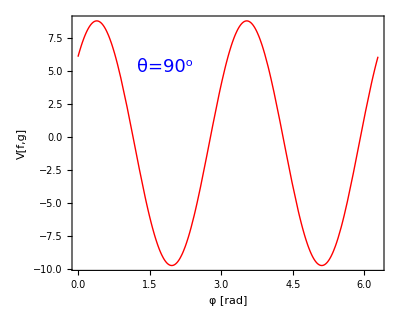

```mathematica
fixedThetaPlot:=Plot[VFunction[f,g]/.{θ->thetaMin},{φ,0,2π},Frame->True,Axes->False,AspectRatio->0.8,FrameStyle->Directive[Black,Thick],PlotStyle->{Red,Thick},LabelStyle->{18,Bold,Black,FontFamily->"Times"},FrameLabel->{"φ [rad]","V[f,g]"},Epilog->Inset[Style[StringTemplate["θ=``^o"][deg[thetaMin]],Blue,18,Italic,FontFamily->"Times"],Scaled[{0.3,0.8}]]];
Show[fixedThetaPlot]
```

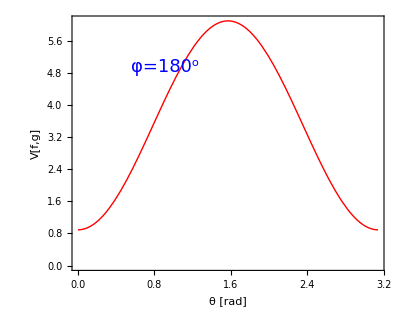

```mathematica
fixedPhiPlot:=Plot[VFunction[f,g]/.{φ->phiMin},{θ,0,π},Frame->True,Axes->False,AspectRatio->0.8,FrameStyle->Directive[Black,Thick],PlotStyle->{Red,Thick},LabelStyle->{18,Bold,Black,FontFamily->"Times"},FrameLabel->{"θ [rad]","V[f,g]"},Epilog->Inset[Style[StringTemplate["φ=``^o"][deg[phiMin]],Blue,18,Italic,FontFamily->"Times"],Scaled[{0.3,0.8}]]];
Show[fixedPhiPlot]
```